```mathematica
QuantumOperator[{"U3",θ,ϕ,λ}]["Matrix"]//Normal//TraditionalForm
```

(cos(θ/2) | -ⅇ^(ⅈ λ) sin(θ/2)
ⅇ^(ⅈ ϕ) sin(θ/2) | cos(θ/2) ⅇ^(ⅈ (λ+ϕ)))

```mathematica
QuantumOperator[{"U3",Pi/2,ϕ,λ}]["Matrix"]//Normal//MatrixForm
```

(1/(√2) | -ⅇ^(ⅈ λ)/(√2)
ⅇ^(ⅈ ϕ)/(√2) | ⅇ^(ⅈ (λ+ϕ))/(√2))

```mathematica
Det[QuantumOperator[{"U3",θ,ϕ,λ}]["Matrix"]]//Simplify
```

ⅇ^(ⅈ (λ+ϕ))

```mathematica
QuantumOperator[{"U2",ω,ϕ}]["Matrix"]//Simplify//Normal//MatrixForm
```

(1/(√2) | -ⅇ^(ⅈ ϕ)/(√2)
ⅇ^(ⅈ ω)/(√2) | ⅇ^(ⅈ (ϕ+ω))/(√2))

```mathematica
CoordinateTransformData
```

```mathematica
MatrixExp[-I/2 ω Total[Table[PauliMatrix[i],{i,3}]CoordinateTransformData["Spherical"->"Cartesian","Mapping", {1,θ,φ}]]]/.θ->Pi/2//FullSimplify//TrigToExp//FullSimplify//MatrixForm
```

(Cos[ω/2] | (-ⅈ Cos[φ]-Sin[φ]) Sin[ω/2]
(-ⅈ Cos[φ]+Sin[φ]) Sin[ω/2] | Cos[ω/2])

{0,0,1}

-Graphics3D-

```mathematica
QuantumState[{1,0}]//TraditionalForm
```

0

```mathematica
Manipulate[mat=Chop[(MatrixExp[-I/2 ω Total[Table[PauliMatrix[i],{i,3}]CoordinateTransformData["Spherical"->"Cartesian","Mapping", {1,Pi/2,ϕ}]]])];GraphicsColumn[{Show[{ParametricPlot3D[Evaluate[m1=Chop[(MatrixExp[-I/2 ω1 Total[Table[PauliMatrix[i],{i,3}]CoordinateTransformData["Spherical"->"Cartesian","Mapping", {1,Pi/2,ϕ}]]])];
ρ=KroneckerProduct[m1.{1,0},Conjugate[m1.{1,0}]];
Table[Tr[ρ.PauliMatrix[i]],{i,3}]],{ω1,0,ω}],QuantumState[mat.{1,0}]["BlochPlot"],Graphics3D[{Pink,Thick,Line[{CoordinateTransformData["Spherical"->"Cartesian","Mapping", {1.2,Pi/2,ϕ}],-CoordinateTransformData["Spherical"->"Cartesian","Mapping", {1.2,Pi/2,ϕ}]}]}]},Axes->False,PlotRange->All,AxesOrigin->{0,0,0}],TraditionalForm[QuantumState[QuantumState[mat.{1,0}]]]}],{{ω,0.01},0,2Pi},{ϕ,0,Pi}]
```

```mathematica
Graphics3D[Polygon[{{0,0,0},{0.1,0.1,1},{0,0.1,0.1},{0.1,0,0}}]]
```

```mathematica
BlockchainPut
```

```mathematica
Total[Table[PauliMatrix[i],{i,3}]CoordinateTransformData["Spherical"->"Cartesian","Mapping", {1,θ,φ}]]
```

{{Cos[θ],Cos[φ] Sin[θ]-ⅈ Sin[θ] Sin[φ]},{Cos[φ] Sin[θ]+ⅈ Sin[θ] Sin[φ],-Cos[θ]}}

```mathematica
Det@QuantumOperator[{"U3",θ,ϕ,-ϕ}]["Matrix"]//Normal
```

Cos[θ/2]^2+Sin[θ/2]^2

```mathematica
{#,QuantumBasis[{2,2}][#]}&/@QuantumBasis[{2,2}]["Properties"]
```

{{Association,<|00→{{1,0},{0,0}},01→{{0,1},{0,0}},10→{{0,0},{1,0}},11→{{0,0},{0,1}}|>},{ConjugateTranspose,QuantumBasis[…]},{Diagram,-Graphics-},{Dimension,4},{Dimensions,{2,2}},{Dual,QuantumBasis[…]},{ElementAssociation,<|00→{{1,0},{0,0}},01→{{0,1},{0,0}},10→{{0,0},{1,0}},11→{{0,0},{0,1}}|>},{ElementDimension,4},{ElementDimensions,{2,2}},{ElementNames,{00,01,10,11}},{Elements,{{{1,0},{0,0}},{{0,1},{0,0}},{{0,0},{1,0}},{{0,0},{0,1}}}},{FinalParameters,{}},{FullInputQudits,0},{FullOutputQudits,2},{FullQudits,2},{HasInputQ,False},{InitialParameters,{}},{Input,QuditBasis[…]},{InputBasis,QuantumBasis[…]},{InputDimension,1},{InputDimensions,{}},{InputElementDimension,1},{InputElementDimensions,{}},{InputElementNames,{1}},{InputElements,1},{InputMatrix,SparseArray[…]},{InputNameDimension,1},{InputNameDimensions,{}},{InputQudits,0},{InputRank,0},{InputSize,1},{InputTensor,SparseArray[…]},{Label,None},{LabelHead,None},{Matrix,SparseArray[…]},{MatrixDimensions,{4,4}},{MatrixElementDimensions,{4,1}},{MatrixNameDimensions,{4,1}},{MatrixRepresentation,SparseArray[…]},{NameDimensions,{2,2}},{Names,{00,01,10,11}},{NormalElementNames,{{0,0},{0,1},{1,0},{1,1}}},{OrthogonalElements,{{{1,0},{0,0}},{{0,1},{0,0}},{{0,0},{1,0}},{{0,0},{0,1}}}},{Output,QuditBasis[…]},{OutputBasis,QuantumBasis[…]},{OutputDimension,4},{OutputDimensions,{2,2}},{OutputElementDimension,4},{OutputElementDimensions,{2,2}},{OutputElementNames,{00,01,10,11}},{OutputElements,SparseArray[…]},{OutputMatrix,SparseArray[…]},{OutputNameDimension,4},{OutputNameDimensions,{2,2}},{OutputQudits,2},{OutputRank,2},{OutputSize,4},{OutputTensor,SparseArray[…]},{ParameterArity,0},{Parameters,{}},{ParameterSpec,{}},{Picture,Schrödinger},{Projectors,{{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1}}}},{PureEffects,{QuantumState[…]}},{PureMaps,{{QuantumState[…]},{QuantumState[…]},{QuantumState[…]},{QuantumState[…]}}},{PureStates,{QuantumState[…],QuantumState[…],QuantumState[…],QuantumState[…]}},{QuditBasis,QuditBasis[…]},{Qudits,2},{Rank,2},{Size,5},{Tensor,SparseArray[…]},{TensorDimensions,{2,2,2,2}},{TensorRepresentation,SparseArray[…]},{Transpose,QuantumBasis[…]},{Type,Matrix}}

```mathematica
Array[Symbol[##]&,{2,2}]
```

Symbol::argx: Symbol called with 2 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

{{Symbol[1,1],Symbol[1,2]},{Symbol[2,1],Symbol[2,2]}}

QuantumState[{Cos[θ/2],E^(I ϕ)Sin[θ/2]}]//TraditionalForm

Cos[θ/2] 0+ⅇ^(ⅈ ϕ) 1 Sin[θ/2]

```mathematica
qco/@{QuantumState[…],QuantumState[…],QuantumState[…],QuantumState[…]}//TraditionalForm
```

{00/(√2)+11/(√2),01/(√2)+10/(√2),00/(√2)-11/(√2),01/(√2)-10/(√2)}

```mathematica
Eigenvalues/@(#["DensityMatrix"]&/@Values[(QuantumPartialTrace[#,{1,2}]&/@qss2)]//Normal)//Simplify
```

{{0,1/4 (α Conjugate[α]+β Conjugate[β])},{0,1/4 (α Conjugate[α]+β Conjugate[β])},{0,1/4 (α Conjugate[α]+β Conjugate[β])},{0,1/4 (α Conjugate[α]+β Conjugate[β])}}

```mathematica
QuantumCircuitOperator[{"GroverDiffusion",3}]["Operators"]
```

{QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…]}

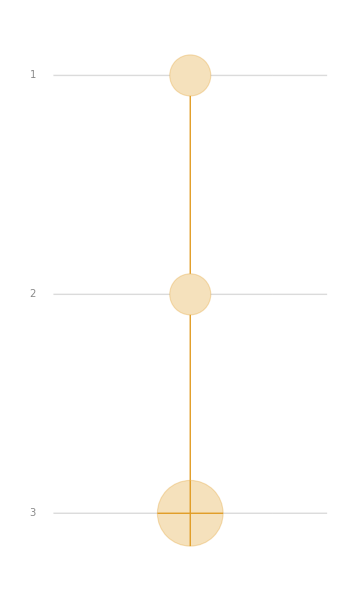

```mathematica
QuantumCircuitOperator[{QuantumOperator[…]}]["Diagram"]
```

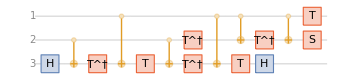

```mathematica
QuantumCircuitOperator["Toffoli"]["Diagram"]
```